```mathematica
(8342.54+2406147(130-1.82^2)^-1 + 15998(38.9-1.82^2)^-1)/10^8
```

0.000277848

```mathematica
Index[p_,t_]:=1+(2.7785 10^-4) *(p(1+p(60.1 - 0.972 t) 10^-10))/(96095.43(1+.003661t))
```

```mathematica
Simple[p_,t_]:=(Index[p,t]-1) 10^8
```

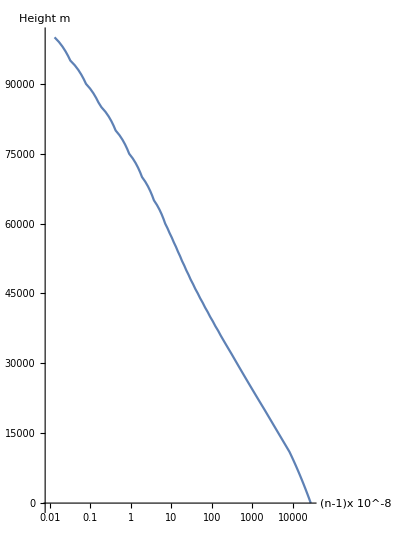

```mathematica
ListLogLinearPlot[
Table[{Simple[QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[x,"Meters"],"Pressure"],"Pascals"]],QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[x,"Meters"],"Temperature"],"Celsius"]]]
,x},{x,0,100000,1000}],AxesLabel->{"(n-1)x 10^-8",Height(m)},Joined->True,GridLines->Automatic,AspectRatio->1.4]
```

```mathematica
tempskew = 0;
```

```mathematica
Index[r_]:=1+Simple[QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-6.371 10^6,"Meters"],"Pressure"],"Pascals"]],QuantityMagnitude[UnitConvert[StandardAtmosphereData[Quantity[r-6.371 10^6,"Meters"],"Temperature"],"Celsius"]]+tempskew] 10^-8
```

```mathematica
(Index[RE]-1)
```

0.000277848

```mathematica
RE = 6.371 10^6;
```

```mathematica
For[r=RE;phi=0;dr=1000;theta=0;,r<RE+100000,r=r+dr,
theta=theta+Pi/2-phi-ArcSin[r/(r+dr)Cos[phi]];
phi=ArcCos[Index[r]/Index[r+dr]*r/(r+dr)Cos[phi]];];theta-phi
```

0.00742063

```mathematica
For[r=RE;phi=0;dr=100;theta=0;,r<RE+100000,r=r+dr,
theta=theta+Pi/2-phi-ArcSin[r/(r+dr)Cos[phi]];
phi=ArcCos[Index[r]/Index[r+dr]*r/(r+dr)Cos[phi]];];theta-phi
```

0.00880987

```mathematica
For[r=RE;phi=0;dr=1;theta=0;,r<RE+100000,r=r+dr,
theta=theta+Pi/2-phi-ArcSin[r/(r+dr)Cos[phi]];
phi=ArcCos[Index[r]/Index[r+dr]*r/(r+dr)Cos[phi]];];theta-phi
```

0.00949116